# Generating New Levels of Super Mario Bros

## Setup

Importing pictures of the first level in each world of Super Mario Bros., the reason I do this is because they’re all overworld style maps to simplify it. I also remove the extra stuff around the image and remove the alpha channel to make sure they’re all consistent.

```mathematica
SetDirectory[$UserDocumentsDirectory];
```

```mathematica
map11 = RemoveAlphaChannel[ImagePad[Import["Wolfram/map11.png"],{{0,0},{-240,0}}]]
map21 = RemoveAlphaChannel[ImagePad[Import["Wolfram/map21.png"],{{0,0},{-240,-240}}]]
map31 = RemoveAlphaChannel[ImagePad[Import["Wolfram/map31.png"],{{0,0},{-240,-240}}]]
map41 = RemoveAlphaChannel[ImagePad[Import["Wolfram/map41.png"],{{0,0},{-240,0}}]]
map51 = RemoveAlphaChannel[ImagePad[Import["Wolfram/map51.png"],{{0,0},{-240,0}}]]
map52 = RemoveAlphaChannel[ImagePad[Import["Wolfram/map52.png"],{{0,0},{-240,-240}}]]
map61 = RemoveAlphaChannel[Import["Wolfram/map61.png"]]
map71 = RemoveAlphaChannel[ImagePad[Import["Wolfram/map71.png"],{{0,0},{-240,0}}]]
map81 = RemoveAlphaChannel[ImagePad[Import["Wolfram/map81.png"],{{0,0},{-240,0}}]]
mapl11 = RemoveAlphaChannel[ImagePad[Import["Wolfram/mapl11.png"],{{0,0},{-240,0}}]]
mapl31 = RemoveAlphaChannel[ImagePad[Import["Wolfram/mapl31.png"],{{0,0},{-240,-240}}]]
mapl41 = RemoveAlphaChannel[ImagePad[Import["Wolfram/mapl41.png"],{{0,0},{-240,-240}}]]
mapl42 = RemoveAlphaChannel[ImagePad[Import["Wolfram/mapl42.png"],{{0,0},{-240,0}}]]
mapl61 = RemoveAlphaChannel[ImagePad[Import["Wolfram/mapl61.png"],{{0,0},{-240,0}}]]
mapl71 = RemoveAlphaChannel[ImagePad[Import["Wolfram/mapl71.png"],{{0,0},{-240,0}}]]
```

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

Here I map the types of blocks to a value

```mathematica
ground = ImageData[ImagePartition[map11,16][[-1]][[1]]]|ImageData[ImagePartition[mapl11,16][[-1]][[1]]];
passthrough = ImageData[ImagePartition[map31,16][[-6]][[85]]];
hard =  ImageData[ImagePartition[map11,16][[-3]][[199]]];
lucky =  ImageData[ImagePartition[map11,16][[-6]][[17]]]|ImageData[ImagePartition[map31,16][[-6]][[17]]];
brick =  ImageData[ImagePartition[map11,16][[-6]][[21]]]|ImageData[ImagePartition[mapl11,16][[6]][[20]]];
tpipe =  ImageData[ImagePartition[map11,16][[-6]][[47]]] | ImageData[ImagePartition[map11,16][[-6]][[48]]] | ImageData[ImagePartition[map51,16]⟦-5⟧[[46]]] | ImageData[ImagePartition[map51,16]⟦-5⟧[[45]]]|ImageData[ImagePartition[map31,16][[-4]][[69]]] |ImageData[ImagePartition[map31,16][[-4]][[68]]];
pipe =  ImageData[ImagePartition[map11,16][[-5]][[47]]] | ImageData[ImagePartition[map11,16][[-5]][[48]]] | ImageData[ImagePartition[map51,16]⟦-4⟧[[46]]] | ImageData[ImagePartition[map51,16]⟦-4⟧[[45]]]|ImageData[ImagePartition[map31,16][[-3]][[69]]]|ImageData[ImagePartition[map31,16][[-3]][[68]]];
bullet = ImageData[ImagePartition[map71,16][[-3]][[20]]]|ImageData[ImagePartition[map71,16][[-3]][[29]]]|ImageData[ImagePartition[map71,16][[-3]][[47]]];
```

```mathematica
ConvertBlocks[image_]:=Switch[ImageData[image],ground,1,hard,1,lucky,1,brick,1,pipe|tpipe,1,bullet,1,passthrough,1,Except["else"],0]
```

I then split the maps into arrays of 16px x 16px since the maps are a grid  of 16px x 16px blocks and then associate each block a value.

```mathematica
array11=Map[ConvertBlocks,ImagePartition[map11,16],{2}];
array21=Map[ConvertBlocks,ImagePartition[map21,16],{2}];
array31=Map[ConvertBlocks,ImagePartition[map31,16],{2}] ;
array41=Map[ConvertBlocks,ImagePartition[map41,16],{2}];
array51=Map[ConvertBlocks,ImagePartition[map51,16],{2}];
array61=Map[ConvertBlocks,ImagePartition[map61,16],{2}];
array71=Map[ConvertBlocks,ImagePartition[map71,16],{2}];
array81=Map[ConvertBlocks,ImagePartition[map81,16],{2}];
arrayl11 = Map[ConvertBlocks, ImagePartition[mapl11,16],{2}];
arrayl31 = Map[ConvertBlocks, ImagePartition[mapl31,16],{2}];
arrayl41 = Map[ConvertBlocks, ImagePartition[mapl41,16],{2}];
arrayl42 = Map[ConvertBlocks, ImagePartition[mapl42,16],{2}];
arrayl61 = Map[ConvertBlocks, ImagePartition[mapl61,16],{2}];
arrayl71 = Map[ConvertBlocks, ImagePartition[mapl71,16],{2}];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImagePartition[map51,16]⟦-5⟧[[46]]
```

-Graphics-

```mathematica
Map[ConvertBlocks,ImagePartition[ImageRotate[map11,-90Degree],16],{2}] (* consider *)
```

## Sequence Predict

My lazy first attempt for the project was to just try and using sequence predict for every row of the level, I was also considering doing it for column but decided against it and moved on to doing a GAN.

```mathematica
sp1=SequencePredict[Partition[array21[[1]],1]];
sp2=SequencePredict[Partition[array21[[2]],1]];
sp3=SequencePredict[Partition[array21[[3]],1]];
sp4=SequencePredict[Partition[array21[[4]],1]];
sp5=SequencePredict[Partition[array21[[5]],1]];
sp6=SequencePredict[Partition[array21[[6]],1]];
sp7=SequencePredict[Partition[array21[[7]],1]];
sp8=SequencePredict[Partition[array21[[8]],1]];
sp9=SequencePredict[Partition[array21[[9]],1]];
sp10=SequencePredict[Partition[array21[[10]],1]];
sp11=SequencePredict[Partition[array21[[11]],1]];
sp12=SequencePredict[Partition[array21[[12]],1]];
sp13=SequencePredict[Partition[array21[[13]],1]];
sp14=SequencePredict[Partition[array21[[14]],1]];
sp15=SequencePredict[Partition[array21[[15]],1]];
```

It found the pattern for the ground which was pretty good.

```mathematica
ArrayPlot[{sp1[{0},"RandomNextElement"->239],sp2[{0},"RandomNextElement"->239],sp3[{0},"RandomNextElement"->239],sp4[{0},"RandomNextElement"->239],sp5[{0},"RandomNextElement"->239],sp6[{0},"RandomNextElement"->239],sp7[{0},"RandomNextElement"->239],sp8[{0},"RandomNextElement"->239],sp9[{0},"RandomNextElement"->239],sp10[{0},"RandomNextElement"->239],sp11[{0},"RandomNextElement"->239],sp12[{0},"RandomNextElement"->239],sp13[{0},"RandomNextElement"->239],sp14[{1},"RandomNextElement"->239],sp15[{1},"RandomNextElement"->239]}]
```

-Graphics-

## Learn Distribution

```mathematica
ld = LearnDistribution[dataset]
```

LearnedDistribution[…]

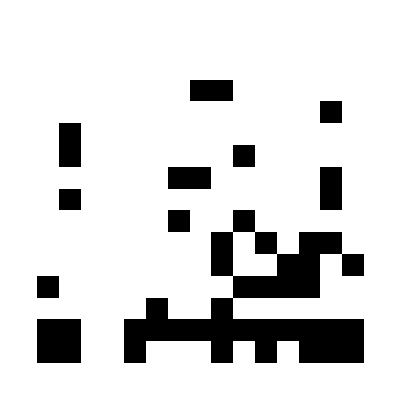

```mathematica
ArrayPlot[RandomVariate[ld][[1]]]
```

# GAN Setup

This was used to figure out how boring a level is but probably won’t use it

```mathematica
boringmap = Join[Table[Table[0,15],13],Table[Table[1,15],2]];
CalculateBoring[image_]:=If[Total[Abs/@Flatten[Subtract[Map[ConvertBlocks,ImagePartition[image,16],{2}],boringmap]]] > 10,image,Nothing]
```

```mathematica
maps ={map11,map21,map31,map41,map51,map52,map61,map71,map81};
```

```mathematica
imagedataset=Flatten[
Table[
Table[ImageTake[map,240,{i,i+240-1}],
{i,1,ImageDimensions[map][[1]]-240+16,16} (* thx isabel*)
],{map,maps}
]
];
```

```mathematica
(* not in use right now because can't figure out input control *)
OneHotConvertBlocks[image_]:=Switch[ImageData[image],ground,{1,0,0},hard,{1,0,0},lucky,{0,1,0},brick,{0,0,1},pipe|tpipe,{1,0,0},bullet,{1,0,0},passthrough,{1,0,0},Except["else"],{0,0,0}]
```

```mathematica
dataset = ArrayReshape[Map[ConvertBlocks,ImagePartition[#,16],{2}],{1,15,15}]&/@imagedataset;
```

```mathematica
Dimensions[dataset]
```

{1956,1,15,15}

This is just for testing the discriminator

```mathematica
datasetrules=Table[entry->1,{entry,dataset}];
```

```mathematica
bad := {Table[Table[RandomInteger[3],15],15]}
```

```mathematica
baddata=Table[{Table[Table[RandomInteger[],15],15]}->0,600];
```

## Discriminator

```mathematica
(* maybe change to leaky relu, check wolfram gan blog post for that *)
```

```mathematica
convolutionBlock[args___]:=NetChain[{ConvolutionLayer[args],NormalizationLayer[],ElementwiseLayer["SELU"],DropoutLayer[0.4]}];
discriminator=NetFlatten@NetChain[{
convolutionBlock[64,{3,3}],
convolutionBlock[64,{3,3}],
LinearLayer[{}],
LogisticSigmoid
},
"Input"->{1,15,15}
]
```

NetChain[<>]

```mathematica
datagen = Join[datasetrules,baddata];
```

```mathematica
(* For testing *) distrained = NetTrain[discriminator,datagen,ValidationSet->Scaled[0.2],MaxTrainingRounds->15]
```

NetTrain::interr2: An unknown internal error occurred. Consult Internal`$LastInternalFailure for potential information.

$Failed

```mathematica
distrained[notdataset[[18]]]
```

## Generator

```mathematica
deconvolutionBlock[args__]:=NetChain[{DeconvolutionLayer[args],NormalizationLayer[],ElementwiseLayer["SELU"],DropoutLayer[0.4]}];
```

```mathematica
generator=NetFlatten@NetChain[{
	{128,3,3},
NormalizationLayer[],ElementwiseLayer["SELU"],DropoutLayer[0.4],
	deconvolutionBlock[64,{5,5}],
	deconvolutionBlock[32,{5,5}],
deconvolutionBlock[1,{5,5}],
ElementwiseLayer[Tanh]
}, "Input"->32,
"Output"->{1,15,15}
]
```

NetChain[<>]

## Putting it all together

```mathematica
gan =NetGANOperator[{generator,discriminator}]
```

NetGANOperator[<>]

```mathematica
getRandomLatent[batchSize_]:=Map[NumericArray[#,"Real32"]&,RandomVariate[NormalDistribution[],{batchSize,32}]]
```

```mathematica
datagen=Function[<|"Sample"->RandomSample[dataset,#BatchSize],"Latent"->getRandomLatent[#BatchSize]|>];
```

A monitor

```mathematica
ShowGeneratedLevels[net_]:=ArrayPlot[Normal[net[["Generator"]][getRandomLatent[1][[1]]]][[1]]]
```

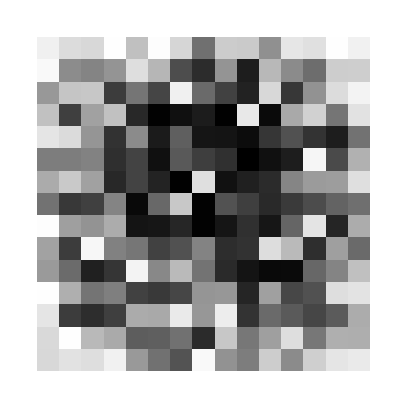

```mathematica
ShowGeneratedLevels[NetInitialize[gan]] (* monitor works nice *)
```

```mathematica
monitoring="";
Dynamic[monitoring]
trained=NetTrain[NetGANOperator[{generator,discriminator}],
{datagen,"RoundLength"->Length[dataset]},
TrainingUpdateSchedule->{"Generator","Discriminator"},
TrainingProgressFunction->{Function[monitoring=ShowGeneratedLevels[#Net]],"Interval"->Quantity [1,"Round"]},
MaxTrainingRounds->40 
]
```

NetGANOperator[<>]

```mathematica
trained[["Discriminator"]][trained[["Generator"]][getRandomLatent[1]]]
```

{0.00204202}

```mathematica
ArrayPlot[Normal[trained[["Generator"]][getRandomLatent[1]]][[1]][[1]]]
```

```mathematica
trained[["Generator"]][getRandomLatent[1]]
```

# Using Learn Distribution and a Discriminator

First train on original, discriminate, any goes to discriminator bad, but above 0.999  go into dataset

```mathematica
baddata=Table[{Table[Table[RandomInteger[],15],15]}->0,600];
```

```mathematica
maps ={map11,map21,map31,map41,map51,map52,map61,map71,map81};
imagedataset=Flatten[
Table[
Table[ImageTake[map,240,{i,i+240-1}],
{i,1,ImageDimensions[map][[1]]-240+16,16} (* thx isabel*)
],{map,maps}
]
];
discdataset = ArrayReshape[Map[ConvertBlocks,ImagePartition[#,16],{2}],{1,15,15}]&/@imagedataset;
lddataset = Map[ConvertBlocks,ImagePartition[#,16],{2}]&/@imagedataset;
```

```mathematica
datasetrules=Table[entry->1,{entry,discdataset}];
```

```mathematica
goodld={};
ldlist={};
ldsetrules={};
datagen={};
```

```mathematica
convolutionBlock[args___]:=NetChain[{ConvolutionLayer[args],NormalizationLayer[],ElementwiseLayer["SELU"],DropoutLayer[0.4]}];
discriminator=NetFlatten@NetChain[{
convolutionBlock[64,{3,3}],
convolutionBlock[64,{3,3}],
LinearLayer[{}],
LogisticSigmoid
},
"Input"->{1,15,15}
]
```

NetChain[<>]

```mathematica
Table[
ldsetrules=Table[entry->0,{entry,ldlist}];
datagen = Join[datasetrules,baddata,ldsetrules];
distrained = NetTrain[discriminator,datagen,ValidationSet->Scaled[0.2]];
ld = LearnDistribution[Join[lddataset,goodld]];
Table[
randomld = {RandomVariate[ld]};
If[distrained[randomld]>0.999,goodld=Append[goodld,randomld[[1]]]];
ldlist=Append[ldlist,randomld];
,20]
,10]
```

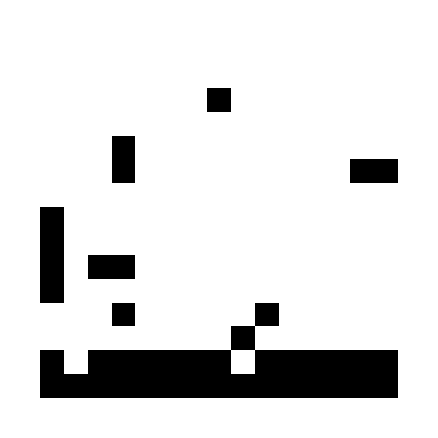

```mathematica
ArrayPlot[RandomVariate[ld]]
```

Tip from stephen: find the features of a standard mario level

# Under construction

```mathematica
NetGANOperator
```

```mathematica
getRandomLatent[32]
```

32

```mathematica
notimages=Table[
Table[
CalculateBoring[Flatten[ImagePartition[map,240]][[i]]],
{i,1,Length[Flatten[ImagePartition[map,240]]]}
],
{map,maps}
]//Flatten
```

```mathematica
Map[ConvertBlocks,ImagePartition[imagedataset[[1]],16],{2}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
notdataset = ArrayReshape[Map[ConvertBlocks,ImagePartition[#,16],{2}],{1,15,15}]&/@notimages;
```

```mathematica
notimages[[18]]
```

-Graphics-

```mathematica
ImageDimensions[map11]
```

{3376,240}

```mathematica
Table[ImageTake[map81,240,{i,i+240-1}],{i,1,ImageDimensions[map81][[1]]-240+16,16}]
```

{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
Length[imagedataset]
```

1757

```mathematica
convolutionBlock[args___]:=NetChain[{ConvolutionLayer[args],NormalizationLayer[],ElementwiseLayer["SELU"],DropoutLayer[0.4]}];
discriminator=NetFlatten@NetChain[{convolutionBlock[64,{4,4},"Stride"->{2,2}],convolutionBlock[64,{4,4},"Stride"->{2,2}],LinearLayer[{}],LogisticSigmoid},"Input"->{1,15,15}]
```

NetChain[<>]

```mathematica
deconvolutionBlock[args___]:=NetChain[{DeconvolutionLayer[args],NormalizationLayer[],ElementwiseLayer["SELU"],DropoutLayer[0.4]}];
generator=NetFlatten@NetChain[{
	{128,5,5},NormalizationLayer[],ElementwiseLayer["SELU"],DropoutLayer[0.4],
	deconvolutionBlock[128,{4,4},"Stride"->{2,2}],
	deconvolutionBlock[128,{4,4},"Stride"->{2,2}],
	ConvolutionLayer[1,{12,12}], ElementwiseLayer[Tanh]
}, "Input"->100,"Output"->{1,15,15}]
```

NetChain[<>]

```mathematica
getRandomLatent[batchSize_]:=Map[NumericArray[#,"Real32"]&,RandomVariate[NormalDistribution[],{batchSize,100}]]
datagen=Function[<|"Sample"->RandomSample[dataset,#BatchSize],"Latent"->getRandomLatent[#BatchSize]|>];
```

```mathematica
trained=NetTrain[NetGANOperator[{generator,discriminator}],
{datagen,"RoundLength"->Length[dataset]},
TrainingUpdateSchedule->{"Discriminator","Generator"},
MaxTrainingRounds->10
]
```

```mathematica
ConvertBack[array_]:=Map[Switch[],Abs[Round[Normal[array]]][[1]][[1]],{2}]
```

{{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,0,0,0,0},{0,0,1,1,0,1,1,1,1,1,0,1,0,0,0},{0,0,0,0,0,0,1,0,1,1,0,0,1,1,0},{0,0,0,1,0,1,1,1,1,0,1,0,0,1,0},{0,0,0,1,0,1,1,1,1,1,0,1,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,1,0},{0,1,1,1,1,1,1,0,1,1,0,1,1,0,1},{0,1,1,1,1,1,1,1,1,1,0,1,1,0,0},{0,0,1,1,1,1,1,1,1,1,0,1,1,0,0},{0,0,0,1,1,1,0,0,0,1,0,1,1,1,0},{0,1,0,1,1,1,1,1,0,0,1,0,0,0,0},{0,0,1,1,0,0,1,1,1,1,0,0,0,0,0},{0,0,1,0,0,0,0,1,1,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0}}

LearnedDistribution[…]

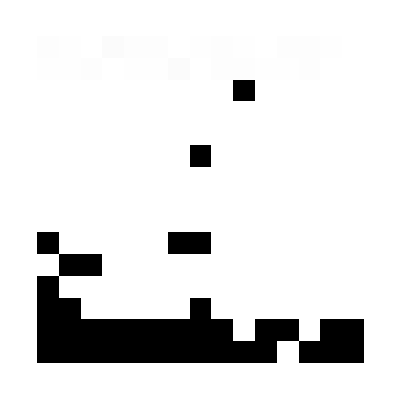

```mathematica
Abs[Round[Normal[NetInitialize[generator][getRandomLatent[1]]]]][[1]][[1]]
```

```mathematica
Dimensions[Table[entry[[15]],{entry,dataset}]]
```

{3747,15}

```mathematica
sp = SequencePredict[lddataset]
```

StringForm::sfr: Item 2 requested in "Invalid training data type (`1`).SequencePredict can not conform the data to any valid type (`2`) for selected method(s)." out of range; 1 items available.

SequencePredict::invinpttyp: Invalid training data type (BooleanTensor).SequencePredict can not conform the data to any valid type (`2`) for selected method(s).

```mathematica
x="hello
yep"
```

hello
yep

```mathematica
CloudDeploy[ExportForm[-Graphics-,"PNG"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/1993bd2f-d0b9-44ec-83ec-9e538491dc2a]

CloudObject[https://www.wolframcloud.com/obj/353633ec-e377-4e69-9e62-c6706633d7cd]

CloudObject[https://www.wolframcloud.com/obj/d4791678-fb0f-493b-8644-65a3daa12c09]

CloudObject[https://www.wolframcloud.com/obj/a0861449-e825-42bd-a06d-e56cdced80a8]

CloudObject[https://www.wolframcloud.com/obj/65664715-e560-432d-918c-b7be4509ecb0]

CloudObject[https://www.wolframcloud.com/obj/02a7838b-6ac5-4491-a550-6414c3fdd40c]

CloudObject[https://www.wolframcloud.com/obj/bb972b44-0a50-480b-90a5-042e4487d72f]

CloudObject[https://www.wolframcloud.com/obj/2a8960ac-f087-4151-a73d-28f17ad0f96f]

CloudObject[https://www.wolframcloud.com/obj/916d095e-05ba-4759-a8ae-491755b9f94a]

CloudObject[https://www.wolframcloud.com/obj/17d83563-90ef-4dc9-b97e-51883ffdaccc]

CloudObject[https://www.wolframcloud.com/obj/6bfbbb3f-cd90-4df1-adc4-4646cc14fb22]

CloudObject[https://www.wolframcloud.com/obj/9bc488a8-13ba-48e6-a60d-3f03f80c9e8b]

CloudObject[https://www.wolframcloud.com/obj/9efa1c36-2e01-42f1-8537-ba46c5f4f81a]

CloudObject[https://www.wolframcloud.com/obj/ac4c0aef-6687-4f31-a240-462039f34d96]

-Graphics-

```mathematica
CloudImport[["https://www.wolframcloud.com/obj/bb972b44-0a50-480b-90a5-042e4487d72f"](https://www.wolframcloud.com/obj/bb972b44-0a50-480b-90a5-042e4487d72f)]
```

-Graphics-

```mathematica
CloudDeploy[Import["Wolfram/Archive.zip"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/8a20a190-adf2-43af-bb84-f897fa997681]

```mathematica
CloudImport[["https://www.wolframcloud.com/obj/8a20a190-adf2-43af-bb84-f897fa997681"](https://www.wolframcloud.com/obj/8a20a190-adf2-43af-bb84-f897fa997681)]
```

Notebook[{Cell[BoxData[RowBox[{{,RowBox[{"mapl61.png",,,"__MACOSX/._mapl61.png",,,"mapl71.png",,,"__MACOSX/._mapl71.png"}],}}]],Output]},FrontEndVersion→13.1 for Mac OS X x86 (64-bit) (June 21, 2022),StyleDefinitions→Default.nb]